```mathematica
Quit[];
```

```mathematica
(*diseased state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*assume tau_s=tau_g*);
```

```mathematica
(* Rescaled System's coefficients and function definition *)
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_]:={
-u[[1]]+f1[tu+ac*ud[[1]]+bc*ud[[2]]],
-u[[2]]+f2[tv+cc*ud[[1]]+dc*ud[[2]]]}
```

```mathematica
(*equilibrium point*)
eq={u,v}/.FindRoot[F[{u,v},{u,v}]=={0,0},{{u,0},{v,0}}]
```

{20.4425,21.8366}

```mathematica
(*characteristic parameter values*)
alpha=ac*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]+dc*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
beta=(ac*dc-bc*cc)*f1'[tu+ac*eq[[1]]+bc*eq[[2]]]*f2'[tv+cc*eq[[1]]+dc*eq[[2]]]
```

-2.53928

11.2213

```mathematica
(*verify the position of the point (alpha,beeta) with respect to the parabola alpha^2=4 beta -> the point is ABOVE the parabola*)
beta-alpha^2/4
```

9.60928

```mathematica
(*Dirac kernel - Laplace transform and related functions defined in paper*)
H[z_]:=Exp[-z];
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2 Cos[w]-(2 w Sin[w])/t;(*given explicitely for ease of computation*)
be[t_,w_]:=1+w^2/t^2;(*given explicitely for ease of computation*)
Co[t_,w_]:=Re[H[I*w]];
rho[w_]:=1; (*given explicitely for ease of computation*)
theta[w_]:=w; (*given explicitely for ease of computation*)
w1[t_]:=w/.FindRoot[Im[Q[t,I*w]]==0,{w,Pi/2,Pi}];
mu[w_]:=1/(rho[w]*Cos[theta[w]]);
```

```mathematica
(*Use Theorem 2.8 for the Dirac kernel, to detect critical value of time delay and frequency - along the curve (gamma_tau) -> ABOVE the parabola*)
{Tau,wtau}={t,w}/.FindRoot[{alpha==al[t,w],beta==be[t,w]},{{t,1},{w,Pi/2}}]
```

{0.216411,0.69188}

```mathematica
(*predicted frequency of oscillations at Hopf bifurcation - divided by Tau due to relation between \Delta and \hat{\Delta}*)
freq=wtau/(Tau*2*Pi)
```

0.50883

```mathematica
(*frequency at bifurcation - rescaled - in Hz*)
freq/(tauS*10^(-3))
```

84.8049

```mathematica
(*stability region for Dirac kernel, together with point of coordinates (alpha, beta) - uses range accoring to bifurcation values, so that domains can be compared*)
pd[t_]:=
Show[RegionPlot[y>1/Co[t,w1[t]]*(x-1/Co[t,w1[t]])&&y>x-1&&x<2(Cos[t*Sqrt[y-1]]-Sqrt[y-1]*Sin[t*Sqrt[y-1]]),{x,2*mu[w1[t]],2},{y,mu[w1[t]],0.96*mu[w1[t]]^2},PlotPoints->100],
Plot[x-1,{x,1+1/Co[t,w1[t]],2},PlotStyle->Red],
Graphics[{Red,PointSize[0.04],Point[{alpha,beta}]}],
LabelStyle->Directive[Bold,Black, FontSize->20],ImageSize->{Automatic,300},
Epilog->Inset[Framed[Style[Row[{"Dirac, τ=",t}],Bold,20],Background->LightYellow,RoundingRadius->4],{1+mu[w1[Tau]],0.85*mu[w1[Tau]]^2}],
PlotRange->{{2*mu[w1[Tau]],2},{mu[w1[Tau]],0.96*mu[w1[Tau]]^2}}]
```

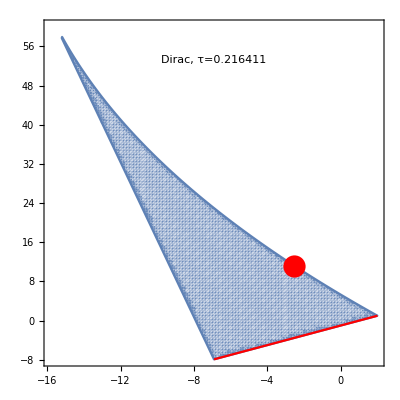

```mathematica
pd[Tau]
```

```mathematica
(*system with DIRAC kernel*)
sys[tau_]:={u'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[2]],
 u[t /; t≤ 0]==0,
v[t /; t≤ 0]==0};
```

```mathematica
(*frequency at Hopf bifurcation computed based on the numerically evaluated solution - agrees with theoretically calculated value*)
Tmax=200;
pts[tau_]:=Reap[s=NDSolve[{u'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[1]],
v'[t]==F[{u[t],v[t]},{u[t-tau],v[t-tau]}][[2]],
 u[t /; t≤ 0]==eq[[1]]*1.1,
v[t /; t≤ 0]==eq[[2]]*1.1,WhenEvent[v'[t]==0,Sow[t]]},{v,v'},{t,Tmax*0.8,Tmax}]][[2,1]];
frequency[tau_]:=1/Mean[Differences[pts[tau],1,2]]
```

```mathematica
frequency[Tau]/(tauS*10^(-3))
```

84.7668

```mathematica
(*frequency comupter numerically at bifurcation - rescaled - in Hz*)
frequency[0.7483]/(tauS*10^(-3))
```

30.286

```mathematica
(*frequency computation for a range of time delays*)
pfreqdiseased=Table[{del,frequency[del]/(tauS*10^(-3))},{del,Tau,4,0.05}];
```

```mathematica
(*plot frequencies for Helthy and Diseased cases, "pfreqhealthy" is computed in the Parkinson_dirac_healthy.nb file*)
Show[ListPlot[pfreqdiseased,Joined->True,PlotRange->All,PlotStyle->{Thick,Red}],ListPlot[pfreqhealthy,Joined->True,PlotRange->All,PlotStyle->{Thick,Blue}],RegionPlot[13<y<30,{x,-0.5,4.5},{y,10,90},PlotStyle->{Green,Opacity[0.2]},PlotLegends->Placed[LineLegend[{Blue,Red},{"Healthy","Diseased"}],Above],LabelStyle->Directive[Bold,Black, FontSize->16]],
FrameLabel->{"Δt/τ_s","frequency (Hz)"},Frame->True,Axes->False,PlotRange->{{0,2},{10,85}},
LabelStyle->Directive[Bold,Black, FontSize->16],ImageSize->500,GridLines->{{Tau,0.7483,1.367,1.967},None},GridLinesStyle->Directive[Gray, Dashed,Thick],
Epilog->Inset[Framed[Style[Row[{"Dirac"}],Bold,20],Background->LightYellow,RoundingRadius->4],{1.8,80}]]
```

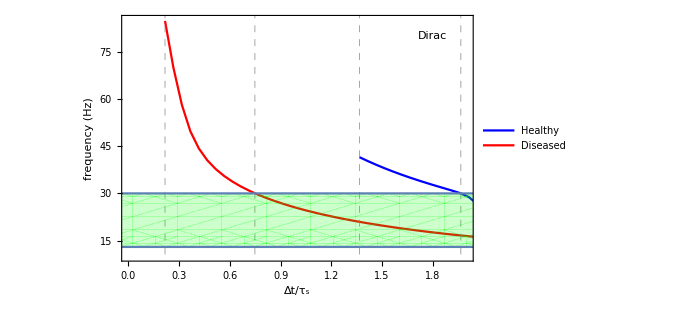
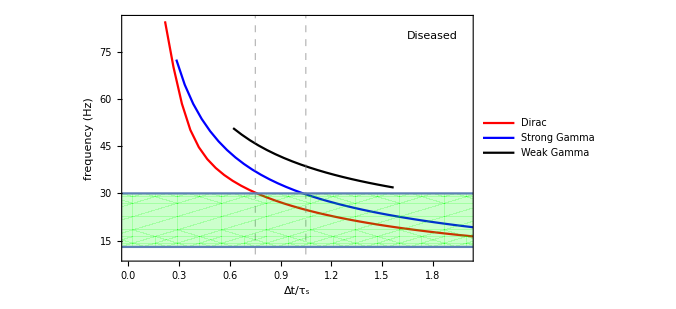

```mathematica
(*plot frequencies for Diseased cases for 3 kernels, "pfreqStrong" is computed in the Parkinson_strong_diseased.nb file, "pfreqWeak" is computed in the Parkinson_weak_diseased.nb file*)
Show[ListPlot[pfreqdiseased,Joined->True,PlotRange->All,PlotStyle->{Thick,Red}],ListPlot[pfreqStrong,Joined->True,PlotRange->All,PlotStyle->{Thick,Blue}],
ListPlot[pfreqWeak,Joined->True,PlotRange->All,PlotStyle->{Thick,Black}],RegionPlot[13<y<30,{x,-0.5,4.5},{y,10,90},PlotStyle->{Green,Opacity[0.2]},PlotLegends->Placed[LineLegend[{Red,Blue,Black},{"Dirac","Strong Gamma","Weak Gamma"}],Above],LabelStyle->Directive[Bold,Black, FontSize->16]],
FrameLabel->{"Δt/τ_s","frequency (Hz)"},Frame->True,Axes->False,PlotRange->{{0,2},{10,85}},
LabelStyle->Directive[Bold,Black, FontSize->16],ImageSize->500,GridLines->{{0.75,1.05},None},GridLinesStyle->Directive[Gray, Dashed,Thick],
Epilog->Inset[Framed[Style[Row[{"Diseased"}],Bold,20],Background->LightYellow,RoundingRadius->4],{1.8,80}]]
```

-Graphics-

```mathematica
(*plot evolution of state variables*)
trans=0;Tmax=160/1.2;
p1[tau_]:=Plot[Evaluate[{u[(t+trans)/(tauS*10^(-3))],v[(t+trans)/(tauS*10^(-3))]} /. NDSolve[sys[tau],{u,v},{t,Tmax}]],{t,0,(Tmax-trans)*tauS*10^(-3)},PlotRange->All,Axes->False,Frame->True, PlotStyle->{{Thick,Red},{Thick,Blue}},FrameLabel->{None,"STN, GP vs. time (s)"},ImageSize->{Automatic,300},LabelStyle->Directive[Bold,Black, FontSize->20]]
```

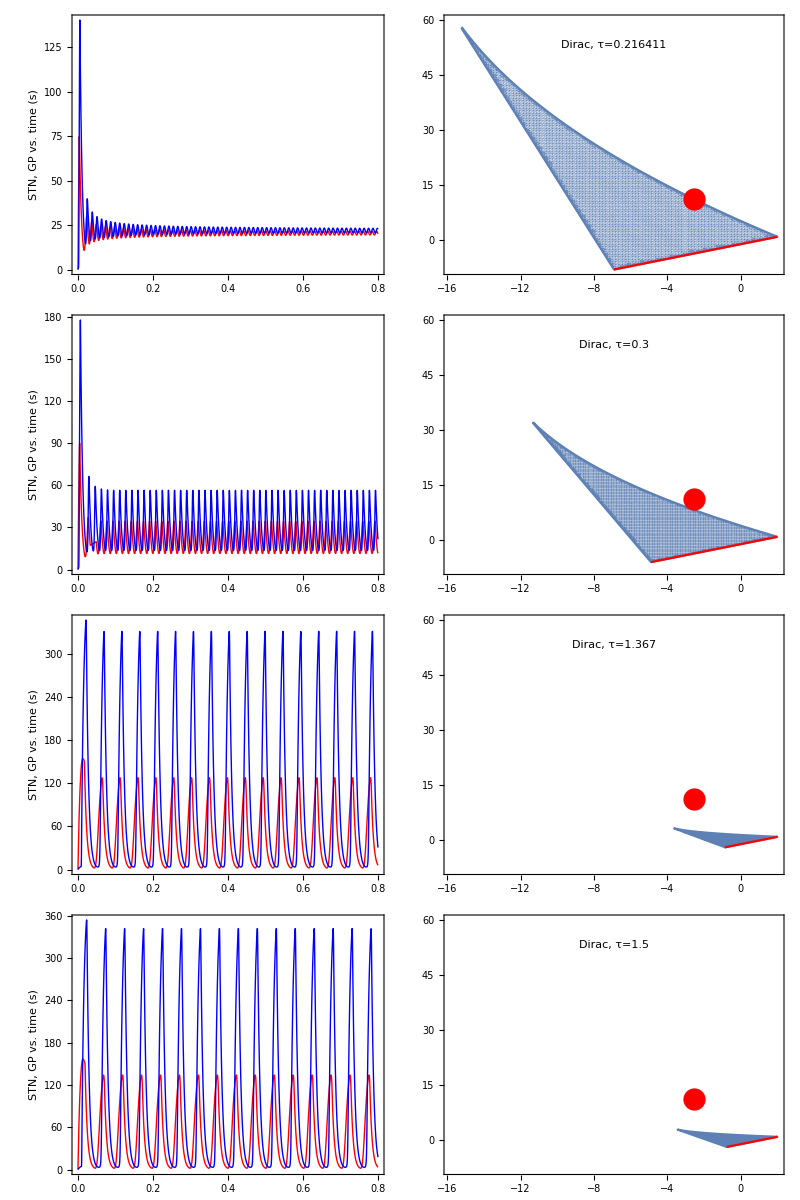

```mathematica
(*Graphics: evolution of state variables vs. stability domain*)
Grid[{{p1[Tau],pd[Tau]},{p1[0.3],pd[0.3]},{p1[1.367],pd[1.367]},{p1[1.5],pd[1.5]}}]
```

```mathematica
Tmax = 100;
trans=0; (* parkinsonian state *) 
p2[tau_]:=ParametricPlot[Evaluate[{u[(t+trans)],v[(t+trans)]} /. NDSolve[sys[tau],{u,v},{t,Tmax}]],{t,0,Tmax-trans},Axes->False,Frame->True,AspectRatio->1,PlotRange->All,PlotLabel->Row[Style[#,14] & /@{"τ=",tau}],LabelStyle->Directive[Bold,Black, Larger], ColorFunction->(ColorData[{"LightTemperatureMap","Reversed"}][#3]&), ImageSize->{Automatic,300},FrameStyle->Directive[FontSize->14]]
```

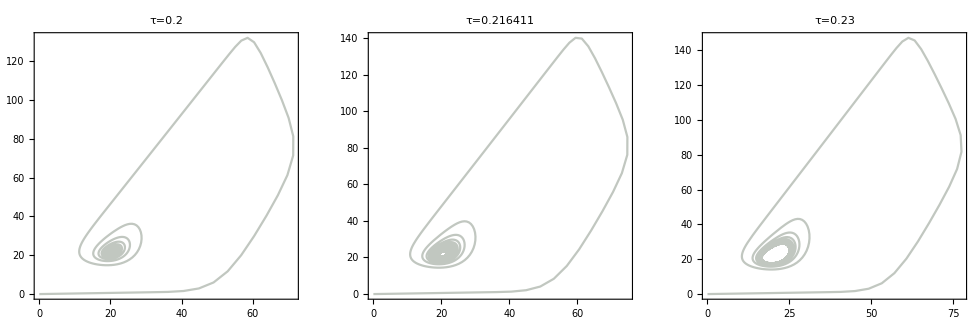

```mathematica
Show[GraphicsGrid[{{p2[0.2],p2[Tau], p2[0.23]}}]]
```